## Axion off-diagonal couplings to quarks and leptons

Goal: 
	Data analysis
	
Input: 
	output/yukawa_quark.m
	output/yukawa_lepton.m
	
Output:
	Figure 4
	Figure 5

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[StringDrop[NotebookDirectory[],-4]]
```

H:\2_Programming\physics\5d_flavourful_axion

```mathematica
<<"WarpFlavourAxion`"
```

WARNING! DO NOT EVALUATE THE WHOLE NOTEBOOK!

### Import Data

```mathematica
quarkData = <<"output/yukawa_quark.m";
Print["Number of Yu Yd 3x3 matrix pairs"]
Dimensions[quarkData]
```

Number of Yu Yd 3x3 matrix pairs

{1321,2,3,3}

```mathematica
leptonData = <<"output/yukawa_lepton.m";
Print["Number of Yn Ye 3x3 matrix pairs (normal hierarchy)"]
Dimensions[leptonData[[1]]]
Print["Number of Yn Ye 3x3 matrix pairs (inverted hierarchy)"]
Dimensions[leptonData[[2]]]
```

Number of Yn Ye 3x3 matrix pairs (normal hierarchy)

{4330,2,3,3}

Number of Yn Ye 3x3 matrix pairs (inverted hierarchy)

{}

### Find a set of c_P, c_M, convert to c_L, c_R

WARNING! THESE RESULTS HAVE BEEN SAVED! 
DO NOT EVALUATE AGAIN

```mathematica
(* 
	Scan the values for Subscript[c, L], Subscript[c, R] for all quarks 
	for different values of cM
	store in cuData, cdData
 *)
```

```mathematica
cMArray=Range[-6.25,6.25,0.5]
With[{seed=0.4},
cuData={};
cdData={};
Do[
yu = quarkData[[i, 1]]; yd = quarkData[[i,2]];myu=Minors[yu];myd=Minors[yd];
AppendTo[cuData,
Table[
TurnLeft[({cM,cP}/.FindRoot[FermionProfileBulkOverlapCM[cP,cM]==QuarkEffYukawa[yu,yd,myu,myd][#],{cP,Norm[cM]+seed}]&)/@{"u","c","t"}],
{cM,cMArray}
]//Quiet
];
AppendTo[cdData,
Table[
TurnLeft[({cM,cP}/.FindRoot[FermionProfileBulkOverlapCM[cP,cM]==QuarkEffYukawa[yu,yd,myu,myd][#],{cP,Norm[cM]+seed}]&)/@{"d","s","b"}],
{cM,cMArray}
]//Quiet
],{i,Length[quarkData]}
]
];//AbsoluteTiming
Clear[yu,yd,myu,myd]
Dimensions[cuData]
Dimensions[cdData]
```

{-6.25,-5.75,-5.25,-4.75,-4.25,-3.75,-3.25,-2.75,-2.25,-1.75,-1.25,-0.75,-0.25,0.25,0.75,1.25,1.75,2.25,2.75,3.25,3.75,4.25,4.75,5.25,5.75,6.25}

{274.392,Null}

{1321,26,3,2}

{1321,26,3,2}

```mathematica
(* 
	Scan the values for Subscript[c, L], Subscript[c, R] for all leptons
	for different values of cM
	store in clNHData, clIHData
 *)
```

```mathematica
With[{seed=0.4},
clNHData={};
Do[
yn = leptonData[[1]][[i, 1]]; ye = leptonData[[1]][[i,2]];myn=Minors[yn];mye=Minors[ye];
AppendTo[clNHData,
Table[
TurnLeft[({cM,cP}/.FindRoot[FermionProfileBulkOverlapCM[cP,cM]==LeptonEffYukawa[yn,ye,myn,mye][#],{cP,Norm[cM]+seed}]&)/@{"e","mu","tau"}],
{cM,cMArray}
]//Quiet
],{i,Length[leptonData[[1]]]}]
];//AbsoluteTiming
Clear[yn,ye,myn,mye];
Dimensions[clNHData]
```

{446.411,Null}

{4330,26,3,2}

```mathematica
(*
With[{seed=0.001},
clIHData={};
Do[
yn = leptonData[[2]][[i, 1]]; ye = leptonData[[2]][[i,2]];myn=Minors[yn];mye=Minors[ye];
AppendTo[clIHData,
Table[
TurnLeft[({cM,cP}/.FindRoot[FermionProfileBulkOverlapCM[cP,cM]==LeptonEffMass[yn,ye,myn,mye][#],{cP,cM+seed}]&)/@{"e","mu","tau"}],
{cM,cMArray}
]//Quiet
],{i,Length[leptonData[[2]]]}]
];//AbsoluteTiming
Clear[yn,ye,myn,mye];
Dimensions[clIHData]
*)
```

{398.896,Null}

{3975,21,3,2}

```mathematica
(* Export all evaluated result *)
```

```mathematica
Export["output/cLcR03.m",{cMArray,cuData,cdData,clNHData}]
```

output/cLcR03.m

```mathematica
data= Import["output/cLcR02.m"];
```

```mathematica
{cMArray,cuData,cdData,clNHData}=data;
```

```mathematica
Dimensions[cuData]
```

{1321,41,3,2}

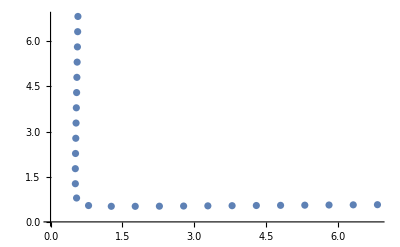

```mathematica
(* 
Sanity check
*)
ListPlot[cuData[[3,All,3,All]]]
```

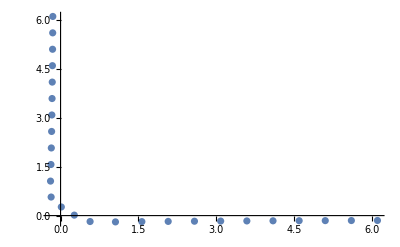

```mathematica
ListPlot[clNHData[[1,All,1,All]]]
```